```mathematica
Needs["PlotLegends`"]
```

## Procedures generiques

### Vol Deterministe

```mathematica
LocalVolCall[CC_,CCDev1_,CCDev2_,CCInvInteg_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav},
fav=(F+K)/2;
w=1/(√(2 T))(CCInvInteg[K]-CCInvInteg[F]);
H1=2(ⅇ^(-w^2)+√(π w^2)(NormDis[√2 Abs[w]-1]));
H2=2/3(ⅇ^(-w^2)(1-2 w^2)-2(Abs[w])^3 √π(NormDis[√2 Abs[w]]-1));
Q=CC[fav]^2/4((CCDev2[fav]/CC[fav])-1/2(CCDev1[fav]/CC[fav])^2);
Max[F-K,0]+(√(CC[K] CC[F] T))/(2 √(2π))(H1+T H2 Q)
]
```

```mathematica
LocalVolBSVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav,b1,b2,b3},
fav=(F+K)/2;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
Log[K/F]/(CCInvInteg[K]-CCInvInteg[F])(1+T (b3))
]
```

### Vol Stochastique

```mathematica
StochVolBSVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_,fav_]:=Module[{w,H1,H2,Q,b1,b2,b3,x,z},
b1=1/24 ν^2 (2-3 ρ^2);
b2=1/4 CCDev1[fav] ν ρ;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
z=(CCInvInteg[F]-CCInvInteg[K]);
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[F-K]<10^-7,Abs[CC[F]]/F(1+T (b1+b2+b3)),Abs[Log[F/K]/x] (1+T (b1+b2+b3))]
]
```

```mathematica
StochVolNormVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_,fav_]:=Module[{w,H1,H2,Q,b1,b2,b3,x,z},
b1=1/24 ν^2 (2-3 ρ^2);b2=1/4 CCDev1[fav] ν ρ;b3=1/24  (2 CCDev2[fav]CC[fav]-(CCDev1[fav])^2+CC[fav]^2);
z=CCInvInteg[F]-CCInvInteg[K];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[F-K]<10^-7,Abs[CC[F]] (1+T (b1+b2+b3)),Abs[(K-F)/x] (1+T (b1+b2+b3))]]
```

## Hagan SABR

```mathematica
SABRHaganBSVol[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,x,Effetmat},z=(f^(1-β)-K^(1-β))/(α (1-β));
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Effetmat=(1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T)/(1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920);
If[z==0,K^(-1+β) α Effetmat,
α/(f K)^((1-β)/2) z/x  Effetmat  ]]
```

```mathematica
SABRHaganCallBSOption[F_,α_,β_,ρ_,ν_,K_,T_]:=BS[F,K,T,SABRHaganBSVol[F,K,α,T,β,ρ,ν]]
```

```mathematica
SABRHaganCallBSDigitale[F_,α_,β_,ρ_,ν_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=SABRHaganCallBSOption[F,α,β,ρ,ν,K+shift,T];
s2=SABRHaganCallBSOption[F,α,β,ρ,ν,K-shift,T];
(s2-s1)/(2shift)
]
```

```mathematica
SABRHaganNormVol[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,x,Effetmat,b1,b2,b3,fav},
z=(f^(1-β)-K^(1-β))/(α (1-β));fav=(f+K)/2;
b1=1/24 ν^2 (2-3 ρ^2);
b2=1/4 α β fav^(β-1) ν ρ;
b3=1/24 fav^(-2+2 β) α^2 (β-1)^2;
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[f-K]<10^-7,Abs[α f^β] (1+T (b1+b2+b3)),Abs[(K-f)/x] (1+T (b1+b2+b3))]]
```

```mathematica
SABRHaganCallNormOption[F_,α_,β_,ρ_,ν_,K_,T_]:=BS[F,K,T,SABRHaganNormVol[F,K,α,T,β,ρ,ν]]
```

```mathematica
SABRHaganCallNormDigitale[F_,α_,β_,ρ_,ν_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=SABRHaganCallNormOption[F,α,β,ρ,ν,K+shift,T];
s2=SABRHaganCallNormOption[F,α,β,ρ,ν,K-shift,T];
(s2-s1)/(2shift)
]
```

## Pure SABR

```mathematica
SABRCC[F_,alpha_,beta_]:=alpha F^beta
```

```mathematica
SABRCCDev1[F_,alpha_,beta_]:=alpha beta F^(beta-1)
```

```mathematica
SABRCCDev2[F_,alpha_,beta_]:=alpha  beta (beta-1)F^(beta-2)
```

```mathematica
SABRCCInvInteg[F_,alpha_,beta_]:=F^(1-beta)/((1-beta)alpha)
```

### Pricing

```mathematica
SABRCallBSVol[F_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{fav=F},
StochVolBSVol[(SABRCC[#,α,β])&,(SABRCCDev1[#,α,β])&,(SABRCCDev2[#,α,β])&,(SABRCCInvInteg[#,α,β])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
SABRCallBSOption[F_,α_,β_,ρ_,ν_,K_,T_]:=BS[K,K,T,SABRCallBSVol[F,α,β,ρ,ν,K,T]]
```

```mathematica
SABRCallBSDigitale[F_,α_,β_,ρ_,ν_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=SABRCallBSOption[F,α,β,ρ,ν,K+shift,T];
s2=SABRCallBSOption[F,α,β,ρ,ν,K-shift,T];
(s2-s1)/(2shift)
]
```

```mathematica
SABRCallNormVol[F_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{fav=(F+K)/2},
StochVolNormVol[(SABRCC[#,α,β])&,(SABRCCDev1[#,α,β])&,(SABRCCDev2[#,α,β])&,(SABRCCInvInteg[#,α,β])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
SABRCallNormOption[F_,α_,β_,ρ_,ν_,K_,T_]:=NormalCall[F,SABRCallNormVol[F,α,β,ρ,ν,K,T],K,T]
```

```mathematica
SABRCallNormDigitale[F_,α_,β_,ρ_,ν_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=SABRCallNormOption[F,α,β,ρ,ν,K+shift,T];
s2=SABRCallNormOption[F,α,β,ρ,ν,K-shift,T];
(s2-s1)/(2shift)]
```

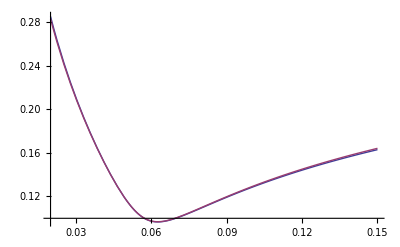

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Plot[{SABRCallBSVol[f,α,β,ρ,ν,K,T],SABRHaganBSVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15}]]
```

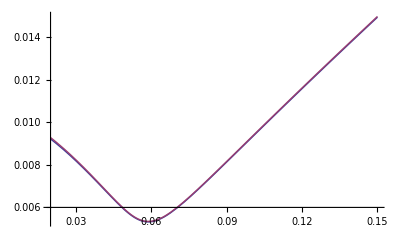

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Plot[{SABRCallNormVol[f,α,β,ρ,ν,K,T],SABRHaganNormVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15}]]
```

## Epsilon SABR

### Definition de la vol Loc

```mathematica
ESABRCC[F_,alpha_,beta_,ϵ_]:=alpha (ϵ+F)^beta
```

```mathematica
ESABRCCDev1[F_,alpha_,beta_,ϵ_]:=alpha beta (ϵ+F)^(beta-1)
```

```mathematica
ESABRCCDev2[F_,alpha_,beta_,ϵ_]:=alpha  beta (beta-1)(ϵ+F)^(beta-2)
```

```mathematica
ESABRCCInvInteg[F_,alpha_,β_,ϵ_]:=(F ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F^2/ϵ])/alpha
```

### Pricing

```mathematica
ESABRCallBSVol[F_,K_,vol_,T_,beta_,ρ_,ν_,ϵ_]:=
Module[{},
StochVolBSVol[(ESABRCC[#,vol,beta,ϵ])&,(ESABRCCDev1[#,vol,beta,ϵ])&,(ESABRCCDev2[#,vol,beta,ϵ])&,(ESABRCCInvInteg[#,vol,beta,ϵ])&,ρ,ν,F,K,T]
]
```

```mathematica
ESABRCallNormVol[F_,K_,alpha_,T_,beta_,ρ_,ν_,ϵ_]:=
Module[{},
StochVolNormVol[(ESABRCC[#,alpha,beta,ϵ])&,(ESABRCCDev1[#,alpha,beta,ϵ])&,(ESABRCCDev2[#,alpha,beta,ϵ])&,(ESABRCCInvInteg[#,alpha,beta,ϵ])&,ρ,ν,F,K,T,F]
]
```

## Epsilon gamma SABR

### Definition de la vol Loc

```mathematica
EZSABRCC[F_,F0_,α_,β_,ϵ_,γ_]:=α Sech[(F-F0)/γ] (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2)
```

```mathematica
EZSABRCCDev1[F_,F0_,α_,β_,ϵ_,γ_]:=α (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2) ((β (F0+γ Sinh[(F-F0)/γ]))/(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))-(Sech[(F-F0)/γ] Tanh[(F-F0)/γ])/γ)
```

```mathematica
EZSABRCCDev2[F_,F0_,α_,β_,ϵ_,γ_]:=α (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2) (-Sech[(F-F0)/γ]^3/γ^2+((-2+β) β Cosh[(F-F0)/γ] (F0+γ Sinh[(F-F0)/γ])^2)/(ϵ^2 (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ)^2)+(β Cosh[(F-F0)/γ])/(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))-(β (F0+γ Sinh[(F-F0)/γ]) Tanh[(F-F0)/γ])/(γ ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))+(Sech[(F-F0)/γ] Tanh[(F-F0)/γ]^2)/γ^2)
```

```mathematica
EZSABRCCInvInteg[F_,F0_,α_,β_,ϵ_,γ_]:=1/α  ϵ^(-β/2) (Hypergeometric2F1[1/2,β/2,3/2,-(F0+γ Sinh[(F-F0)/γ])^2/ϵ] (F0+γ Sinh[(F-F0)/γ]))
```

### Pricing

```mathematica
EZSABRCallBSVol[F_,α_,β_,ρ_,ν_,ϵ_,γ_,K_,T_]:=
Module[{fav=F},
StochVolBSVol[(EZSABRCC[#,F,α,β,ϵ,γ])&,(EZSABRCCDev1[#,F,α,β,ϵ,γ])&,(EZSABRCCDev2[#,F,α,β,ϵ,γ])&,(EZSABRCCInvInteg[#,F,α,β,ϵ,γ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
EZSABRCallBSOption[F_,α_,β_,ρ_,ν_,ϵ_,γ_,K_,T_]:=BS[K,K,T,EZSABRCallBSVol[F,α,β,ρ,ν,ϵ,γ,K,T]]
```

```mathematica
EZSABRCallBSDigitale[F_,α_,β_,ρ_,ν_,ϵ_,γ_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=EZSABRCallBSOption[F,α,β,ρ,ν,ϵ,γ,K+shift,T];
s2=EZSABRCallBSOption[F,α,β,ρ,ν,ϵ,γ,K-shift,T];
(s2-s1)/(2shift)
]
```

```mathematica
EZSABRCallNormVol[F_,α_,β_,ρ_,ν_,ϵ_,γ_,K_,T_]:=
Module[{fav=F},
StochVolNormVol[(EZSABRCC[#,F,α,β,ϵ,γ])&,(EZSABRCCDev1[#,F,α,β,ϵ,γ])&,(EZSABRCCDev2[#,F,α,β,ϵ,γ])&,(EZSABRCCInvInteg[#,F,α,β,ϵ,γ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
EZSABRCallNormOption[F_,α_,β_,ρ_,ν_,ϵ_,γ_,K_,T_]:=NormalCall[F,EZSABRCallNormVol[F,K,α,T,β,ρ,ν,ϵ,γ],K,T]
```

```mathematica
EZSABRCallNormDigitale[F_,α_,β_,ρ_,ν_,ϵ_,γ_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=EZSABRCallNormOption[F,α,β,ρ,ν,ϵ,γ,K+shift,T];
s2=EZSABRCallNormOption[F,α,β,ρ,ν,ϵ,γ,K-shift,T];
(s2-s1)/(2shift)]
```

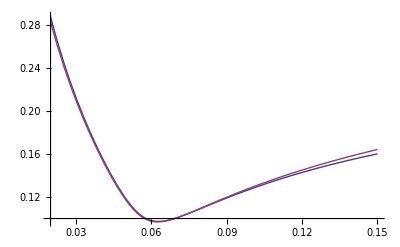

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0001,γ=0.15},
Plot[{EZSABRCallBSVol[f,α,β,ρ,ν,ϵ,γ,K,T],SABRHaganBSVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15}]]
```

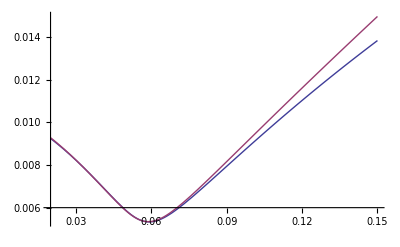

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0001,γ=0.08},
Plot[{EZSABRCallNormVol[f,α,β,ρ,ν,ϵ,γ,K,T],SABRHaganNormVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15}]]
```

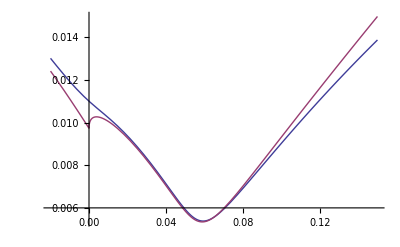

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0002,γ=0.08},
Plot[{EZSABRCallNormVol[f,α,β,ρ,ν,ϵ,γ,K,T],SABRHaganNormVol[f,α,β,ρ,ν,K,T]},{K,-0.02,0.15}]]
```

## Paribas SABR

### Definition de la vol Loc

```mathematica
PSABRCC[F_,K_,α_,β1_,β2_,λ_]:=α ((1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))F^β1+F^β2(1-1/(1+F^(β1-β2)(ⅇ^(λ F)-1))))
```

```mathematica
PSABRCCDev1[F_,K_,α_,β1_,β2_,λ_]:=(ⅇ^(F λ) F^(-1+β1+β2) α (F^β2 β1+(-1+ⅇ^(F λ)) F^β1 β2-F^(1+β1) λ+F^(1+β2) λ))/(((-1+ⅇ^(F λ)) F^β1+F^β2)^2)
```

```mathematica
PSABRCCDev2[F_,K_,α_,β1_,β2_,λ_]:=1/(((-1+ⅇ^(F λ)) F^β1+F^β2)^3)ⅇ^(F λ) F^(-2+β1+β2) α (F^(2 β2) (-1+β1) β1+(-1+ⅇ^(F λ))^2 F^(2 β1) (-1+β2) β2-(-1+ⅇ^(F λ)) F^(β1+β2) (β1+β1^2+β2-4 β1 β2+β2^2)+2 F^(1+2 β2) β1 λ-2 (-1+ⅇ^(F λ)) F^(1+2 β1) β2 λ-2 F^(1+β1+β2) (β1+ⅇ^(F λ) β1+β2-2 ⅇ^(F λ) β2) λ+(1+ⅇ^(F λ)) F^(2+2 β1) λ^2-(2+ⅇ^(F λ)) F^(2+β1+β2) λ^2+F^(2+2 β2) λ^2)
```

```mathematica
PSABRCCInvInteg[F_,K_,α_,β1_,β2_,λ_]:=1/α((F^(1-β2)-K^(1-β2))/(1-β2)+λ^(β1-1) (-Gamma[1-β1,F λ]+Gamma[1-β1,K λ])+λ^(β2-1) (Gamma[1-β2,F λ]-Gamma[1-β2,K λ]))
```

### Pricing

```mathematica
PSABRCallBSVol[F_,α_,β1_,β2_,λ_,ρ_,ν_,K_,T_]:=
Module[{fav=F},
StochVolBSVol[(PSABRCC[F,#,α,β1,β2,λ])&,(PSABRCCDev1[F,#,α,β1,β2,λ])&,(PSABRCCDev2[F,#,α,β1,β2,λ])&,(PSABRCCInvInteg[F,#,α,β1,β2,λ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
PSABRCallBSOption[F_,α_,β1_,β2_,λ_,ρ_,ν_,K_,T_]:=BS[K,K,T,PSABRCallBSVol[F,α,β1,β2,λ,ρ,ν,K,T]]
```

```mathematica
PSABRCallBSDigitale[F_,α_,β1_,β2_,λ_,ρ_,ν_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=PSABRCallBSOption[F,α,β1,β2,λ,ρ,ν,K+shift,T];
s2=PSABRCallBSOption[F,α,β1,β2,λ,ρ,ν,K-shift,T];
(s2-s1)/(2shift)
]
```

```mathematica
PSABRCallNormVol[F_,α_,β1_,β2_,λ_,ρ_,ν_,K_,T_]:=
Module[{fav=F},
StochVolNormVol[(PSABRCC[#,F,α,β1,β2,λ])&,(PSABRCCDev1[#,F,α,β1,β2,λ])&,(PSABRCCDev2[#,F,α,β1,β2,λ])&,(PSABRCCInvInteg[#,F,α,β1,β2,λ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
PSABRCallNormOption[F_,α_,β1_,β2_,λ_,ρ_,ν_,K_,T_]:=NormalCall[F,PSABRCallNormVol[F,α,β1,β2,λ,ρ,ν,K,T],K,T]
```

```mathematica
PSABRCallNormDigitale[F_,α_,β1_,β2_,λ_,ρ_,ν_,K_,T_]:=Module[{s1,s2,shift=0.00001},
s1=PSABRCallNormOption[F,α,β1,β2,λ,ρ,ν,K+shift,T];
s2=PSABRCallNormOption[F,α,β1,β2,λ,ρ,ν,K-shift,T];
(s2-s1)/(2shift)]
```

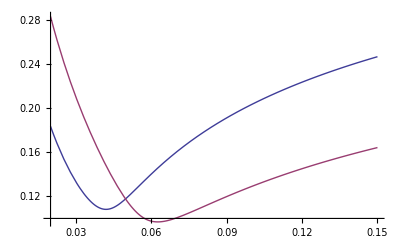

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,β1=0.01,β2=0.5,λ=100,ATMvol,ρ=-0.56,ν=0.45},
Plot[{PSABRCallBSVol[f,α,β1,β2,λ,ρ,ν,K,T],SABRHaganBSVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15},
PlotLegend->{"PSABR","Hagan"},LegendPosition->{1.,-0.5}]]
```

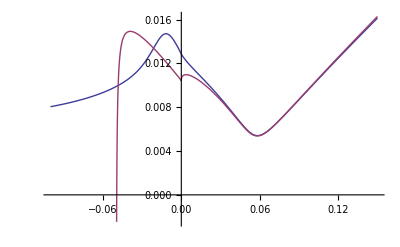

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,β1=0.01,β2=0.5,λ=100,ρ=-0.56,ν=0.5},
Plot[{PSABRCallNormVol[f,α,β1,β2,λ,ρ,ν,K,T],SABRCallNormVol[f,α,β,ρ,ν,K,T]},{K,-0.1,0.15},
PlotLegend->{"PSABR","Hagan"},LegendPosition->{1.,-0.5}]]
```

## Deuxieme Ordre

### Theorie

```mathematica
Le terme de premier et second ordre diagonal sont :
```

```mathematica
Subscript[a, 1](x)=P(x)=R/6+Q
```

```mathematica
Subscript[a, 2](x,x)=1/180(Subscript[R, ijkl] R^ijkl-Subscript[R, ij] R^ij) +(P(x)^2)/2+1/12 Subscript[F, ij] F^ij+1/6 ΔQ+1/30 ΔR
```

```mathematica
ou Subscript[F, ij]=D[Subscript[A, j], i]-D[Subscript[A, i], j]
```

```mathematica
Quand R=0 et que nous somme en dim 1 on a
```

```mathematica
Subscript[a, 1](x)=Q
```

```mathematica
Subscript[a, 2](x,x)=Q^2/2+1/6 ΔQ
```

```mathematica
pour le cas CEV on :
```

```mathematica
Subscript[a, 1](x)=1/8 β(β-2)fav^(2β-2)
```

```mathematica
Subscript[a, 2](x,x)=(β(β-2)(3β-2)(3β-4))/128 fav^(4β-4)
```

### Second ordre avec avec approximation sans courbure pour le second ordre

```mathematica
we assume that
```

```mathematica
p(τ,K,a|0,f,α)=(√g[f, α])/(4π τ)√Δ[K,a,f,α] P[f,α,K,a],aⅇ^((-σ[K,f])/(2τ))(1+a1[K,a,f,α] τ+a2[K,a,f,α] τ^2)
```

```mathematica
Subscript[a, 1](x)=R/6+Q
```

```mathematica
Subscript[a, 2](x,x)=Q^2/2+1/6 ΔQ
```

```mathematica
(labordere p137)  By the Tanaka formula we get :
```

```mathematica
Call[T,K|F0]=Max[F0-K,0]+1/2∫_0^T ⅆτ∫_0^∞ ⅆa a^2 p(τ,K ,a|0,f,α)
```

### Implementation :

```mathematica
StochVolBSVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_,fav_]:=Module[{w,H1,H2,Q,b1,b2,b3,x,z},
b1=1/24 ν^2 (2-3 ρ^2);
b2=1/4 CCDev1[fav] ν ρ;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
z=(CCInvInteg[F]-CCInvInteg[K]);
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[F-K]<10^-7,Abs[CC[F]]/F(1+T (b1+b2+b3)),Abs[Log[F/K]/x] (1+T (b1+b2+b3))]
]
```

```mathematica
StochVolNormVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_,fav_]:=Module[{w,H1,H2,Q,b1,b2,b3,x,z},
b1=1/24 ν^2 (2-3 ρ^2);b2=1/4 CCDev1[fav] ν ρ;b3=1/24  (2 CCDev2[fav]CC[fav]-(CCDev1[fav])^2+CC[fav]^2);
z=CCInvInteg[F]-CCInvInteg[K];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[F-K]<10^-7,Abs[CC[F]] (1+T (b1+b2+b3)),Abs[(K-F)/x] (1+T (b1+b2+b3))]]
```

## Anexe

### Anexe : Second ordre selon avramidi

```mathematica
f[x_]:=1/Tanh[x]-1/x
```

```mathematica
H0[x_]:=(n-1-(n-3)/x f[x])
```

```mathematica
Simplify[D[H0[x],x]-(n-1)/2 f[x]H0[x]]
```

((-3+n) (-1+x Coth[x]))/x^3-1/2 (-1+n) (-1/x+Coth[x]) (-1+n-((-3+n) (-1+x Coth[x]))/x^2)+((-3+n) (-1+x^2 Csch[x]^2))/x^3

```mathematica
H1[x_]:=((-3+n) (-1+x Coth[x]))/x^3-1/2 (-1+n) (-1/x+Coth[x]) (-1+n-((-3+n) (-1+x Coth[x]))/x^2)+((-3+n) (-1+x^2 Csch[x]^2))/x^3
```

```mathematica
Simplify[D[H1[x],x]+((n-1)/2 f[x]+(n-1)/x)H1[x]]
```

1/(4 x^4)((-3+n) (35+x^2+n^2 (1+x^2)-2 n (6+x^2))-(-1+n)^2 x^2 (-3+n-x^2+n x^2) Coth[x]^2+(-3+n) (-1+n)^2 x^3 Coth[x]^3+2 x^2 (21+x^2+n^2 (3+x^2)-2 n (8+x^2)) Csch[x]^2-(-3+n) x Coth[x] (15-8 n+n^2+2 (3+n) x^2 Csch[x]^2))

```mathematica
B[x_]:=1/(4 x^4)((-3+n) (35+x^2+n^2 (1+x^2)-2 n (6+x^2))-(-1+n)^2 x^2 (-3+n-x^2+n x^2) Coth[x]^2+(-3+n) (-1+n)^2 x^3 Coth[x]^3+2 x^2 (21+x^2+n^2 (3+x^2)-2 n (8+x^2)) Csch[x]^2-(-3+n) x Coth[x] (15-8 n+n^2+2 (3+n) x^2 Csch[x]^2))
```

```mathematica
∫_0^(ρ r) x B[x]ⅆx
```

1/4 (1/6 (93-127 n+59 n^2-9 n^3)-1/(4 r^2 ρ^2)Csch[r ρ]^2 (105-71 n+15 n^2-n^3+30 r^2 ρ^2+14 n r^2 ρ^2-14 n^2 r^2 ρ^2+2 n^3 r^2 ρ^2+r^4 ρ^4-3 n r^4 ρ^4+3 n^2 r^4 ρ^4-n^3 r^4 ρ^4+(-105-r^4 ρ^4+n^3 (1+r^4 ρ^4)-3 n^2 (5+r^4 ρ^4)+n (71+3 r^4 ρ^4)) Cosh[2 r ρ]-2 (-3+n) r ρ (15+r^2 ρ^2+n^2 (1+r^2 ρ^2)-2 n (4+r^2 ρ^2)) Sinh[2 r ρ]))

```mathematica
Simplify[-((n-1)ρ)/(2 r^2)1/4 (1/6 (93-127 n+59 n^2-9 n^3)-1/(4 r^2 ρ^2)Csch[r ρ]^2 (105-71 n+15 n^2-n^3+30 r^2 ρ^2+14 n r^2 ρ^2-14 n^2 r^2 ρ^2+2 n^3 r^2 ρ^2+r^4 ρ^4-3 n r^4 ρ^4+3 n^2 r^4 ρ^4-n^3 r^4 ρ^4+(-105-r^4 ρ^4+n^3 (1+r^4 ρ^4)-3 n^2 (5+r^4 ρ^4)+n (71+3 r^4 ρ^4)) Cosh[2 r ρ]-2 (-3+n) r ρ (15+r^2 ρ^2+n^2 (1+r^2 ρ^2)-2 n (4+r^2 ρ^2)) Sinh[2 r ρ]))]
```

-1/(8 r^2)(-1+n) ρ (1/6 (93-127 n+59 n^2-9 n^3)-1/(4 r^2 ρ^2)Csch[r ρ]^2 (105-71 n+15 n^2-n^3+30 r^2 ρ^2+14 n r^2 ρ^2-14 n^2 r^2 ρ^2+2 n^3 r^2 ρ^2+r^4 ρ^4-3 n r^4 ρ^4+3 n^2 r^4 ρ^4-n^3 r^4 ρ^4+(-105-r^4 ρ^4+n^3 (1+r^4 ρ^4)-3 n^2 (5+r^4 ρ^4)+n (71+3 r^4 ρ^4)) Cosh[2 r ρ]-2 (-3+n) r ρ (15+r^2 ρ^2+n^2 (1+r^2 ρ^2)-2 n (4+r^2 ρ^2)) Sinh[2 r ρ]))

```mathematica
b2[n_,ρ_,r_]:=-1/(8 r^2)(-1+n) ρ (1/6 (93-127 n+59 n^2-9 n^3)-1/(4 r^2 ρ^2)Csch[r ρ]^2 (105-71 n+15 n^2-n^3+30 r^2 ρ^2+14 n r^2 ρ^2-14 n^2 r^2 ρ^2+2 n^3 r^2 ρ^2+r^4 ρ^4-3 n r^4 ρ^4+3 n^2 r^4 ρ^4-n^3 r^4 ρ^4+(-105-r^4 ρ^4+n^3 (1+r^4 ρ^4)-3 n^2 (5+r^4 ρ^4)+n (71+3 r^4 ρ^4)) Cosh[2 r ρ]-2 (-3+n) r ρ (15+r^2 ρ^2+n^2 (1+r^2 ρ^2)-2 n (4+r^2 ρ^2)) Sinh[2 r ρ]))
```

```mathematica
n=2
```

```mathematica
b1=1/4 ρ^2(1+1/(ρ^2 r^2)(ρ r Coth[ρ r]-1))
```